#### Formatting

```mathematica
Format[ec]:=Subscript[e, c]
Format[m1]:=Subscript[m, 1]
Format[m2]:=Subscript[m, 2]
Format[ec[i_]]:=Subscript[e, i]
Format[e[i_]]:=Subscript[e, i]
Format[p[i_]]:=Subscript[p, i]
Format[a[i_]]:=Subscript[a, i]
Format[ϵ[i_]]:=Subscript[ϵ, i]
Format[ϵ[i_,j_]]:=Subscript[ϵ, i,j]
Format[e[i_,j_]]:=Subscript[e, i,j]
Format[e[i_,j_,k_]]:=Subscript[e, i,j ,k]
Format[p[i_,j_]]:=Subscript[p, {i,j}]
```

#### Definitions

```mathematica
h[x_]:=-x Log[2,x]-(1-x) Log[2,(1-x)]
```

```mathematica
H1[ProbDist_,d_]:=-∑_(i=0)^(d-1) ProbDist[i]Log[2,ProbDist[i]]
H2[ProbDist_,d_]:=-∑_(i=0)^(d-1) ∑_(j=0)^(d-1) ProbDist[i,j]Log[2,ProbDist[i,j]]
H3[ProbDist_,d_]:=-∑_(i=0)^(d-1) ∑_(j=0)^(d-1) ∑_(k=0)^(d-1) ProbDist[i,j,k]Log[2,ProbDist[i,j,k]]
H4[ProbDist_,d_]:=-∑_(i=0)^(d-1) ∑_(j=0)^(d-1) ∑_(k=0)^(d-1) ∑_(l=0)^(d-1) ProbDist[i,j,k,l]Log[2,ProbDist[i,j,k,l]]
```

```mathematica
$Assumptions={Element[k,Integers]}
```

{k∈ℤ}

## Bounding I_nn22 over extended IC

```mathematica
ClearAll[calculateChainInfo,faGen,entropy,getH];

(*1. Shannon Entropy*)
entropy[probs_List]:=Total[Map[If[#===0||#===0.,0,-# Log[2,#]]&,Flatten[probs]]];

(*2. Alice's input function f(a) *)
faGen[v_List]:=Module[{n=Length[v],i=v[[1]],sub=v[[2;;]]},(n-1)-Total[FoldList[Times,Mod[i+sub,2]]]];

(*k:number of variables to keep (including g)*)
getH[n_,ec_,eps_,b_,k_]:=Module[{fullJoint,marginal},(*Create flat joint distribution of 2^(n+1) elements*)fullJoint=Flatten[Table[With[{pBase=(1+(-1)^Mod[Total[c],2] eps)/2^n},pBase*(1+(-1)^Mod[c[[1]]+g,2] ec e[faGen[c],b])/2],{g,0,1},{c,Tuples[{0,1},n]}]];
(*To marginalize down to k variables,we partition into 2^k buckets*)marginal=Total/@Partition[fullJoint,2^(n+1-k)];
entropy[marginal]];

(*4. computing entroipes*)
calculateChainInfo[n_Integer,ec_,eps_]:=Sum[Module[{kVal=k,Hac,Hbc,Habc,Hc},
(*We use the entropy identity for I(g; x_k|x_0...x_{k-1})*)(*g is the external bit; x_0...x_{k-1} is history*)
Hac=getH[n,ec,eps,kVal,kVal+1](*H(g,x_0...x_{k-1})*);
Habc=getH[n,ec,eps,kVal,kVal+2](*H(g,x_0...x_k)*);
(*Note:H(history,x_k) and H(history) are independent of g.They come from the pBase distribution.*)
Hbc=entropy[Total/@Partition[Table[(1+(-1)^Mod[Total[c],2] eps)/2^n,{c,Tuples[{0,1},n]}],2^(n-(kVal+1))]];
Hc=entropy[Total/@Partition[Table[(1+(-1)^Mod[Total[c],2] eps)/2^n,{c,Tuples[{0,1},n]}],2^(n-kVal)]];
Hac+Hbc-Habc-Hc],{k,0,n-1}];
```

```mathematica
Bound[n_]:=Module[{Biases, BiasesConst,InEq},
Biases=Table[e[i-1,j-1],{i,1,n},{j,1,n}]//Flatten;BiasesConst=Table[-1<=e[i-1,j-1]<=1,{i,1,n},{j,1,n}]//Flatten;
InEq=Log[2]D[calculateChainInfo[n,ec,eps],{ec,2}]/.{ec->0,eps->0}//FullSimplify;
MaxValue[{SumIN[n],InEq<=1,BiasesConst},Biases]//Simplify
]
```

```mathematica
InEqOld[n_]:=1/4^n((2e[0,0]+∑_(j=1)^(n-1) 2^j e[j,0])^2+∑_(i=1)^(n-1) (2e[0,i]+∑_(j=1)^(n-i) (-1)^KroneckerDelta[j,n-i] 2^j e[j,i])^2)
InEqNew[n_]:=1/4^n((2e[0,0]+∑_(j=1)^(n-1) 2^j e[j,0])^2+∑_(i=1)^(n-1) 2^(i-1)(2e[0,i]+∑_(j=1)^(n-i) (-1)^KroneckerDelta[j,n-i] 2^j e[j,i])^2)
```

## Mixing Bounds for Isotropic nn22 boxes

```mathematica
IN2[n_]:=Module[
{i,j,s=SparseArray[{},{n+1,n+1}]},
Clear[i];
s[[1,2]]=-1;
For[i=2,i<=n+1,i++,s[[i,1]]=-n-1+i];
For[i=3,i<=n+1,i++,s[[i,n+4-i]]=-1];
For[i=2,i<=n+1,i++,For[j=2,j<=3+n-i,j++,s[[i,j]]=1]];
s]
```

```mathematica
SumIN[N_]:=∑_(i=2)^(N+1) ∑_(j=2)^(N+1) IN2[N][[i,j]](1+e[i-2,j-2])/4+∑_(i=1)^(N+1) (IN2[N][[i,1]]+IN2[N][[1,i]])/2
```

```mathematica
{e[j_,i_]->(2KroneckerDelta[0,Mod[i j,n]]-1)e}
```

```mathematica
RepISOn={e[j_,i_]->(1-2KroneckerDelta[n,i+ j])e};
```

```mathematica
RepISOn={e[j_,i_]->(-KroneckerDelta[i+j,n]e+(1-KroneckerDelta[i+j,n]))};
```

```mathematica
isonn22=(-n^2+n-2)/8+1/4(∑_(i=0)^(n-1) ∑_(j=0)^(n-i-1) e+∑_(i=1)^(n-1) e)
```

1/8 (-2+n-n^2)+1/4 (e (-1+n)+1/2 e n (1+n))

```mathematica
logconstr3=(calculateChainInfo[3,ec,0]-1+h[(1+ec)/2])/.{e[j_,i_]->(1-2KroneckerDelta[3,i+ j])e}//FullSimplify
logconstr4=(calculateChainInfo[4,ec,0]-1+h[(1+ec)/2])/.{e[j_,i_]->(1-2KroneckerDelta[4,i+ j])e}//FullSimplify
logconstr5=(calculateChainInfo[5,ec,0]-1+h[(1+ec)/2])/.{e[j_,i_]->(1-2KroneckerDelta[5,i+ j])e}//FullSimplify
logconstr6=(calculateChainInfo[6,ec,0]-1+h[(1+ec)/2])/.{e[j_,i_]->(1-2KroneckerDelta[6,i+ j])e}//FullSimplify
logconstr7=(calculateChainInfo[7,ec,0]-1+h[(1+ec)/2])/.{e[j_,i_]->(1-2KroneckerDelta[7,i+ j])e}//FullSimplify
logconstr8=(calculateChainInfo[8,ec,0]-1+h[(1+ec)/2])/.{e[j_,i_]->(1-2KroneckerDelta[8,i+ j])e}//FullSimplify
logconstr9=(calculateChainInfo[9,ec,0]-1+h[(1+ec)/2])/.{e[j_,i_]->(1-2KroneckerDelta[9,i+ j])e}//FullSimplify
logconstr10=(calculateChainInfo[10,ec,0]-1+h[(1+ec)/2])/.{e[j_,i_]->(1-2KroneckerDelta[10,i+ j])e}//FullSimplify
```

(-4 e_c ArcTanh[e_c]+10 e e_c ArcTanh[e e_c]-2 Log[1-e_c]-2 Log[1+e_c]+5 (Log[1-e e_c]+Log[1+e e_c]))/Log[16]

(-8 e_c ArcTanh[e_c]+22 e e_c ArcTanh[e e_c]-4 Log[1-e_c]-4 Log[1+e_c]+11 (Log[1-e e_c]+Log[1+e e_c]))/Log[256]

(-16 e_c ArcTanh[e_c]+46 e e_c ArcTanh[e e_c]-8 Log[1-e_c]-8 Log[1+e_c]+23 (Log[1-e e_c]+Log[1+e e_c]))/(16 Log[2])

(-32 e_c ArcTanh[e_c]+94 e e_c ArcTanh[e e_c]-16 Log[1-e_c]-16 Log[1+e_c]+47 (Log[1-e e_c]+Log[1+e e_c]))/(32 Log[2])

(-64 e_c ArcTanh[e_c]+190 e e_c ArcTanh[e e_c]-32 Log[1-e_c]-32 Log[1+e_c]+95 (Log[1-e e_c]+Log[1+e e_c]))/(64 Log[2])

(-128 e_c ArcTanh[e_c]+382 e e_c ArcTanh[e e_c]-64 Log[1-e_c]-64 Log[1+e_c]+191 (Log[1-e e_c]+Log[1+e e_c]))/(128 Log[2])

(-256 e_c ArcTanh[e_c]+766 e e_c ArcTanh[e e_c]-128 Log[1-e_c]-128 Log[1+e_c]+383 (Log[1-e e_c]+Log[1+e e_c]))/(256 Log[2])

(-512 e_c ArcTanh[e_c]+1534 e e_c ArcTanh[e e_c]-256 Log[1-e_c]-256 Log[1+e_c]+767 (Log[1-e e_c]+Log[1+e e_c]))/(512 Log[2])

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

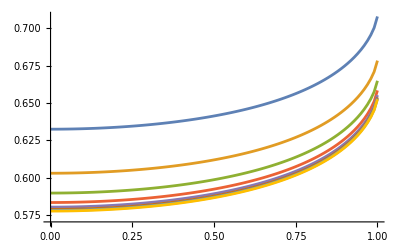

{{1.×10^-10},0.632456}

{{1.×10^-10},0.603023}

{{1.×10^-10},0.589768}

{{1.×10^-10},0.58346}

{{1.×10^-10},0.580382}

{{1.×10^-10},0.57886}

{{1.×10^-10},0.578104}

{{1.×10^-10},0.577727}

```mathematica
g3U[r_]:=e/.FindRoot[(logconstr3/.{ec->r})==0,{e,3/4}]
g4U[r_]:=e/.FindRoot[(logconstr4/.{ec->r})==0,{e,3/4}]
g5U[r_]:=e/.FindRoot[(logconstr5/.{ec->r})==0,{e,3/4}]
g6U[r_]:=e/.FindRoot[(logconstr6/.{ec->r})==0,{e,3/4}]
g7U[r_]:=e/.FindRoot[(logconstr7/.{ec->r})==0,{e,3/4}]
g8U[r_]:=e/.FindRoot[(logconstr8/.{ec->r})==0,{e,3/4}]
g9U[r_]:=e/.FindRoot[(logconstr9/.{ec->r})==0,{e,3/4}]
g10U[r_]:=e/.FindRoot[(logconstr10/.{ec->r})==0,{e,3/4}]

eps=0.0000000001;
res=100;

ArrayChannel=Array[Identity,res,{eps,1-eps}];
ArrayBias3=Array[g3U,res,{eps,1-eps}];
ArrayBias4=Array[g4U,res,{eps,1-eps}];
ArrayBias5=Array[g5U,res,{eps,1-eps}];
ArrayBias6=Array[g6U,res,{eps,1-eps}];
ArrayBias7=Array[g7U,res,{eps,1-eps}];
ArrayBias8=Array[g8U,res,{eps,1-eps}];
ArrayBias9=Array[g9U,res,{eps,1-eps}];
ArrayBias10=Array[g10U,res,{eps,1-eps}];

Val3=Transpose[{ArrayChannel,ArrayBias3}];
Val4=Transpose[{ArrayChannel,ArrayBias4}];
Val5=Transpose[{ArrayChannel,ArrayBias5}];
Val6=Transpose[{ArrayChannel,ArrayBias6}];
Val7=Transpose[{ArrayChannel,ArrayBias7}];
Val8=Transpose[{ArrayChannel,ArrayBias8}];
Val9=Transpose[{ArrayChannel,ArrayBias9}];
Val10=Transpose[{ArrayChannel,ArrayBias10}];


ListLinePlot[{Val3,Val4,Val5,Val6, Val7,Val8,Val9, Val10}]
{ArrayChannel[[Ordering[ArrayBias3,1]]],Min[ArrayBias3]}
{ArrayChannel[[Ordering[ArrayBias4,1]]],Min[ArrayBias4]}
{ArrayChannel[[Ordering[ArrayBias5,1]]],Min[ArrayBias5]}
{ArrayChannel[[Ordering[ArrayBias6,1]]],Min[ArrayBias6]}
{ArrayChannel[[Ordering[ArrayBias7,1]]],Min[ArrayBias7]}
{ArrayChannel[[Ordering[ArrayBias8,1]]],Min[ArrayBias8]}
{ArrayChannel[[Ordering[ArrayBias9,1]]],Min[ArrayBias9]}
{ArrayChannel[[Ordering[ArrayBias10,1]]],Min[ArrayBias10]}
```

```mathematica
combinedData=Join[{ArrayChannel},{ArrayBias3,ArrayBias4,ArrayBias5,ArrayBias6,ArrayBias7,ArrayBias8,ArrayBias9,ArrayBias10}]//Transpose;
Export["all_data.csv",combinedData,"CSV"]
```

all_data.csv